# Final project: Instructor: Ajeet Gary Student: Junchi Chu Topics: affine cipher, MATH406 Truth False table ,MATH310 Cayley table visualization,MATH403 Fermat little theorem,MATH456 Mean value theorem,MATH410 Diophantine Equation,MATH406

MATH406 NUMbeR THEORY: 
Affine Cipher 


If you want to send a private messeage to someone but someone else want to steal your information, what would you do?

You could do a encrption!!!



how does that work?

lets say you convert english letter from A-Z to 0-25,suppose a function y=ax+b(mod26)
,then plug in all your letters to obtain another sequence of english letters. If someone steal your message but without the key, there is no way to decode it!

Limitations: gcd(a,26)=1?WHY??
Lets find the key first, so we want to find
x=cy+d(mod26)
From y=ax+b → y-b=ax →x=(1/a)x-(b/a)
(1/a)*a=1(mod26) hence gcd(a,26)=1

```mathematica
Grid[{{"a","b","c","d","e","f","g","h","i","j","k","l","m","n","o","p","q","r","s","t","u","v","w","x","y","z"},{"0","1","2","3","4","5","6","7","8","9","10","11","12","13","14","15","16","17","18","19","20","21","22","23","24","25"}},Background->Pink,Frame->True]
```

```mathematica
{{"a", "b", "c", "d", "e", "f", "g", "h", "i", "j", "k", "l", "m", "n", "o", "p", "q", "r", "s", "t", "u", "v", "w", "x", "y", "z"}, {"0", "1", "2", "3", "4", "5", "6", "7", "8", "9", "10", "11", "12", "13", "14", "15", "16", "17", "18", "19", "20", "21", "22", "23", "24", "25"}}



alphabet0="abcdefghijklmnopqrstuvwxyz";
key[n_]:=Table[StringTake[alphabet0,{i}] -> StringTake[alphabet0,{Mod[i-1+n,26]+1}],{i,1,26}];
shift[plaintext_,n_]:= StringReplace[plaintext, key[n]];
affkey[m_,n_]:=Table[StringTake[alphabet0,{i}] -> StringTake[alphabet0,{Mod[m*(i-1)+n,26]+1}],{i,1,26}];
Myaffine[t_,m_,n_]:= StringReplace[t, affkey[m,n]];
Solutionkey[t_,m_,n_]:=Myaffine[t,PowerMod[m,-1,26],-n*PowerMod[m,-1,26]]
(*code source/reference :Professor Larry Washington's web page. Check this out for more encrption method!*)
secret0="mathematicaiscoolthing"
secret1="iamfromcantonbutidontspeakcantonese"
secret2="wedonttalkanymorewedonttalkanmorewedonttalkanymorelikeweusetobe"
secret3="stephencurryismyfavoritebasketballplayer"
secret4="iloveyou"
secret5="ihateyou"

Myaffine[secret0,3,79]
Myaffine[secret1,17,70]
Myaffine[secret2,5,23]
Myaffine[secret3,7,41]
Myaffine[secret4,13,22]
Myaffine[secret5,13,22]
```

a | b | c | d | e | f | g | h | i | j | k | l | m | n | o | p | q | r | s | t | u | v | w | x | y | z
0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25

mathematicaiscoolthing

iamfromcantonbutidontspeakcantonese

wedonttalkanymorewedonttalkanmorewedonttalkanymorelikeweusetobe

stephencurryismyfavoritebasketballplayer

iloveyou

ihateyou

lbgwnlbgzhbzdhrrigwzot

ysozvwoasfdwfjudyrwfdmnisgasfdwfimi

drmpkooxavxknfperdrmpkooxavxkfperdrmpkooxavxknfperalvrdrtjropcr

lsrqmrcdzeebtlvbypgjetsrwplhrswpooqopbre

wjwjwwww

wjwjwwww

wnvbcnngpwbgdjupboobkazofgroztwgraorg

ysozvwoasfdwfjudyrwfdmnisgasfdwfimi

uepwrjjpeerrmrxoogerrxuuarjxmxnjpgrvrrujmphopexdxn

lsrqmrcdzeebtlvbypgjetsrwplhrswpooqopbre

wjwjwwww

wjwjwwww

```mathematica
Solutionkey["lbgwnlbgzhbzdhrrigwzot",3,79]
Solutionkey["ysozvwoasfdwfjudyrwfdmnisgasfdwfimi",17,70]
Solutionkey["drmpkooxavxknfperdrmpkooxavxkfperdrmpkooxavxknfperalvrdrtjropcr",5,23]
Solutionkey["lsrqmrcdzeebtlvbypgjetsrwplhrswpooqopbre",7,41]
```

mathematicaiscoolthing

iamfromcantonbutidontspeakcantonese

wedonttalkanymorewedonttalkanmorewedonttalkanymorelikeweusetobe

stephencurryismyfavoritebasketballplayer

```mathematica
MATH310 Mathematical Proof: 
TRUTH FALSE TABLE
```

```mathematica
AND[x_,y_]:=If[(StringMatchQ[x,"T"]&&StringMatchQ[y,"T"]),T,F];
OR[x_,y_]:=If[(StringMatchQ[x,"F"]&&StringMatchQ[y,"F"]),F,T];
NE[x_]:=If[StringMatchQ[x,"T"],F,T];
XOR[x_,y_]:=If[(StringMatchQ[x,"T"]&&StringMatchQ[y,"T"])||(StringMatchQ[x,"F"]&&StringMatchQ[y,"F"]),F,T];
NOR[x_,y_]:=If[(StringMatchQ[x,"F"]&&StringMatchQ[y,"F"]),T,F];
NAND[x_,y_]:=If[(StringMatchQ[x,"T"]&&StringMatchQ[y,"T"]),F,T];
IMPLIES[x_,y_]:=If[(StringMatchQ[x,"T"]&&StringMatchQ[y,"F"]),F,T];




Grid[{{x,y,x&&y,x||y,!x,x xor y , x nor y, x nand y, x-> y},{"T","T",AND["T","T"],OR["T","T"],NE["T"],XOR["T","T"],NOR["T","T"],NAND["T","T"],IMPLIES["T","T"]},{"T","F",AND["T","F"],OR["T","F"],NE["T"],XOR["T","F"],NOR["T","F"],NAND["T","F"],IMPLIES["T","F"]},{"F","T",AND["F","T"],OR["F","T"],NE["F"],XOR["F","T"],NOR["F","T"],NAND["F","T"],IMPLIES["F","T"]},{"F","F",AND["F","F"],OR["F","F"],NE["F"],XOR["F","F"],NOR["F","F"],NAND["F","F"],IMPLIES["F","F"]}},Frame->All,Background->{{{Blue,Purple}},Pink},Background->{Blue,{{Purple,Purple}}},ItemStyle->White]
```

x | y | x&&y | x||y | !x | x xor y | nor x y | nand x y | x→y
T | T | T | T | F | F | F | F | T
T | F | F | T | F | T | F | T | F
F | T | F | T | T | T | F | T | T
F | F | F | F | T | F | T | T | T

```mathematica
Grid[{{x,y,z,"(x xor !(y nand z))→(x and y)or !z" },{"T","T","F",IMPLIES[ToString[XOR["T",ToString[NE[ToString[NAND["T","F"]]]]]],ToString[OR[ToString[AND["T","T"]],ToString[NE["F"]]]]]},

{"T","T","T",IMPLIES[ToString[XOR["T",ToString[NE[ToString[NAND["T","T"]]]]]],ToString[OR[ToString[AND["T","T"]],ToString[NE["T"]]]]]},

{"F","F","F",IMPLIES[ToString[XOR["F",ToString[NE[ToString[NAND["F","F"]]]]]],ToString[OR[ToString[AND["F","F"]],ToString[NE["F"]]]]]},

{"T","F","F",IMPLIES[ToString[XOR["T",ToString[NE[ToString[NAND["F","F"]]]]]],ToString[OR[ToString[AND["T","F"]],ToString[NE["F"]]]]]},

{"F","T","F",IMPLIES[ToString[XOR["F",ToString[NE[ToString[NAND["T","F"]]]]]],ToString[OR[ToString[AND["F","T"]],ToString[NE["F"]]]]]},

{"F","F","T",IMPLIES[ToString[XOR["F",ToString[NE[ToString[NAND["F","T"]]]]]],ToString[OR[ToString[AND["F","F"]],ToString[NE["T"]]]]]},

{"T","F","T",IMPLIES[ToString[XOR["T",ToString[NE[ToString[NAND["F","T"]]]]]],ToString[OR[ToString[AND["T","F"]],ToString[NE["T"]]]]]},

{"F","T","T",IMPLIES[ToString[XOR["F",ToString[NE[ToString[NAND["T","T"]]]]]],ToString[OR[ToString[AND["F","T"]],ToString[NE["T"]]]]]}


},Background->{{{Blue,Green}},Yellow},Background->{Blue,{{Green,Red}}},ItemStyle->Purple,

Frame->All]
```

x | y | z | (x xor !(y nand z))→(x and y)or !z
T | T | F | T
T | T | T | T
F | F | F | T
T | F | F | T
F | T | F | T
F | F | T | T
T | F | T | F
F | T | T | F

```mathematica
MATH403 Abstract Algebra: 
Cayley Table
A Cayley table,after the 19th century British mathematician Arthur Cayley,describes the structure of a finite group by arranging all the possible products of all the group's elements in a square table reminiscent of an addition or multiplication table
```

```mathematica
MyCayley[x_,y_,n_]:=Mod[x*y,n]/.{1->"a"}
```

```mathematica
Grid[{{ ,1,2,3,4},{1,MyCayley[1,1,5],MyCayley[1,2,5],MyCayley[1,3,5],MyCayley[1,4,5]},{2,MyCayley[2,1,5],MyCayley[2,2,5],MyCayley[2,3,5],MyCayley[2,4,5]},{3,MyCayley[3,1,5],MyCayley[3,2,5],MyCayley[3,3,5],MyCayley[3,4,5]},{4,MyCayley[4,1,5],MyCayley[4,2,5],MyCayley[4,3,5],MyCayley[4,4,5]}},Frame->All,Background->{{{Blue,Red}},Pink},Background->{Blue,{{Green,Red}}},ItemStyle->White]
```

| 1 | 2 | 3 | 4
1 | a | 2 | 3 | 4
2 | 2 | 4 | a | 3
3 | 3 | a | 4 | 2
4 | 4 | 3 | 2 | a

```mathematica
Grid[{{ ,5,15,25,35},{5,MyCayley[5,5,40],MyCayley[5,15,40],MyCayley[5,25,40],MyCayley[5,35,40]},{15,MyCayley[15,5,40],MyCayley[15,15,40],MyCayley[15,25,40],MyCayley[15,35,40]},
{25,MyCayley[25,5,40],MyCayley[25,15,40],MyCayley[25,25,40],MyCayley[25,35,40]},{35,MyCayley[35,5,40],MyCayley[35,15,40],MyCayley[35,25,40],MyCayley[35,35,40]}},Frame->All,Background->{Blue,{{Green,Red}}},ItemStyle->White]
```

| 5 | 15 | 25 | 35
5 | 25 | 35 | 5 | 15
15 | 35 | 25 | 15 | 5
25 | 5 | 15 | 25 | 35
35 | 15 | 5 | 35 | 25

```mathematica
MATH456 Crypto: 
Fermat little theorem
```

```mathematica
Fermat's little theorem states that if p is a prime number,then for any integer a,the number ap−a is an integer multiple of p.In the notation of modular arithmetic,this is expressed as
a^p=a(mod p). For example,if a=2 and p=7,then 2^7=128,and 128−2=126=7×18 is an integer multiple of 7.

If a is not divisible by p,Fermat's little theorem is equivalent to the statement that a^(p−1)−1 is an integer multiple of p,or in symbols: a^(p-1)=1mod p
```

```mathematica
Mod[10^(71),71]
Mod[999^(3911),3911]
Mod[8^(223),223]
Mod[13^(59),59]
Mod[2^(5),5]

Mod[762^(9397-1),9397]
Mod[10^(71-1),71]
Mod[999^(3911-1),3911]
Mod[8^(223-1),223]
Mod[13^(59-1),59]
Mod[2^(5-1),5]
Mod[762^(9397-1),9397]
```

10

999

8

13

2

1

1

1

«3 more identical outputs»

```mathematica
1
Manipulate[Plot[Mod[IntegerPart[a]^(n),n ],{a,1,600},PlotStyle->{Orange},PlotLabel->Style["Fermat little theorem:a^n=a(mod n) if a <n",FontSize->14],AxesLabel->{"a","a^n"}],{a,1,1000},{n,RandomPrime[10000,600]}]
```

1

```mathematica
Manipulate[Plot[Mod[IntegerPart[a]^(n),n ],{a,1,60000},PlotStyle->{Orange},PlotLabel->Style["Fermat little theorem:a^n=a(mod n) if a>n",FontSize->14],AxesLabel->{"a","a^n"}],{a,1,1000},{n,RandomPrime[10000,600]}]

Manipulate[Plot[Mod[IntegerPart[a]^(n-1),n ],{a,1,6000000},PlotLabel->Style["Fermat little theorem:a^(n-1)=1(mod n) if a>n",FontSize->14],AxesLabel->{"a","a^(n-1)"},PlotStyle->Directive[Red,Specularity[White,40]],Mesh->None],{a,1,10000},{n,RandomPrime[10000,600]}]
Manipulate[Plot[Mod[IntegerPart[a]^(n-1),n ],{a,1,60},PlotLabel->Style["Fermat little theorem:a^(n-1)=1(mod n) if a<n",FontSize->14],AxesLabel->{"a","a^(n-1)"},PlotStyle->Directive[Red,Specularity[White,40]],Mesh->None],{a,1,1000},{n,RandomPrime[10000,600]}]
```

MATH410 advanced calculus : 

  mean value theorem
Suppose f (x) is a function that satisfies both of the following.f (x) is continuous on the closed interval[a, b].f (x) is differentiable on the open interval (a, b)
Then there is a number c such that a < c < b and f′ (c) = f (b) − f (a)/b − a

```mathematica
f[x_]:=x^3+Sin[x];
fs[a_,b_]:=(f[a]-f[b]) /(a-b)

Manipulate[plotc=Plot[(f[a]-f[b]) /(a-b),{x,0,100},PlotLabel->Style["Mean value theorem:f(a)-f(b)/(a-b)",FontSize->14],PlotStyle->{Black}],{a,1,100},{b,0,100}]
Manipulate[plotd=Plot[f'[x],{x,0,100},PlotLabel->Style["Mean value theorem:f'(x)",FontSize->14],PlotStyle->{Orange,Dashed,Thick}],{x,0,100}]
Show[plotc,plotd]//Dynamic
```

Math406 DiophantineEquation :
   Is there possible to have :
   x^3 + y^3 = z^3 for x, y, z all positive integer ?

   
   No!

```mathematica
Dio[x_,y_,z_]:=IntegerPart[x]^3+IntegerPart[y]^3-IntegerPart[z]^3;
Dio[50,68,76]
Manipulate[plotc=Plot[Dio[x,y,z],{x,50,100},AspectRatio->1,PlotLabel->Style["vision for x^3+y^3=z^3",FontSize->14],PlotStyle->Yellow],{y,50,100},{z,50,100
}]
```

456

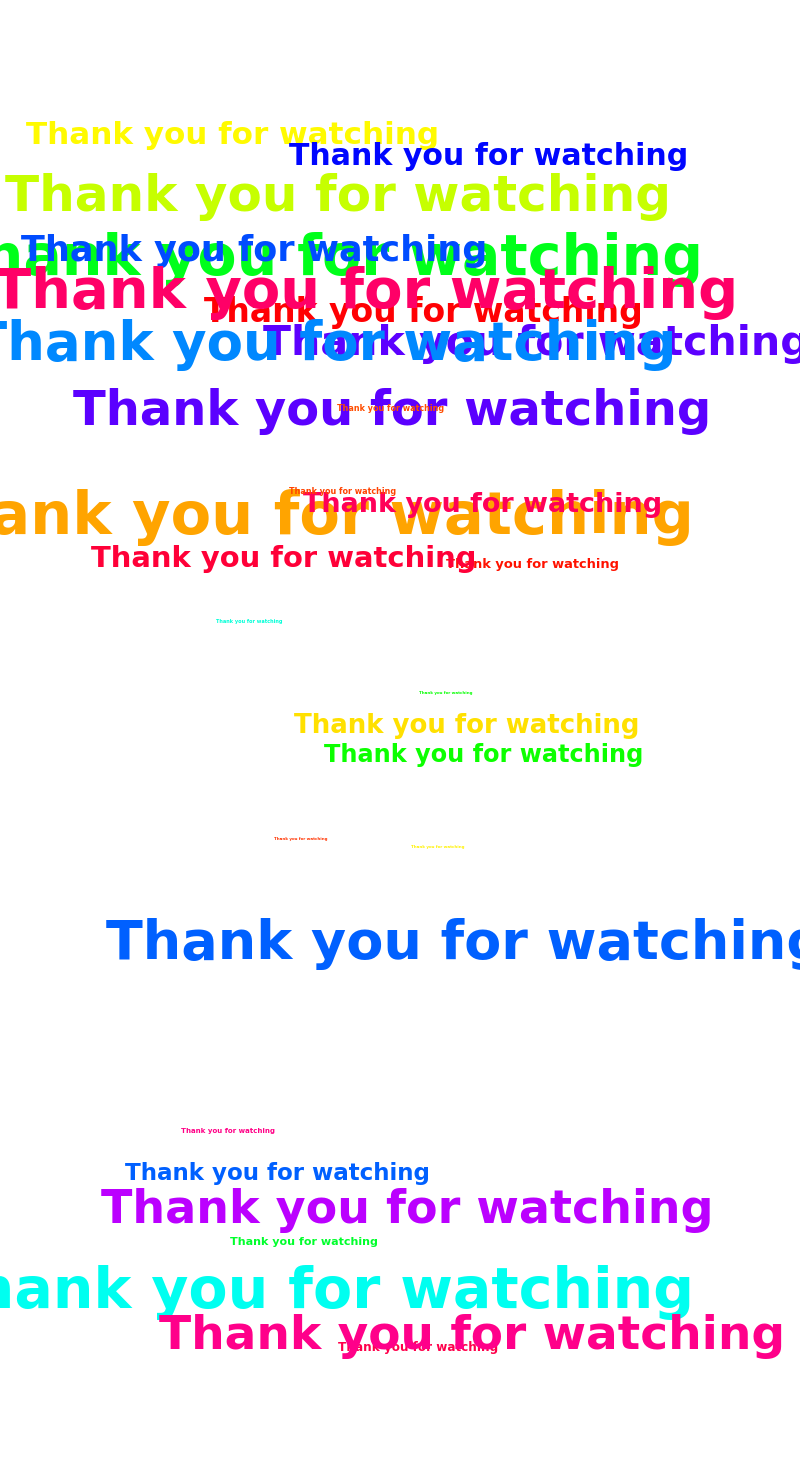

```mathematica
If[1==1,Graphics[Table[Text[Style["Thank you for watching",Hue[RandomReal[]],Italic,Bold,RandomInteger[60]],RandomReal[.1,{2}],Automatic,RandomReal[{-1,1},{2}]],{30}],AspectRatio->3/GoldenRatio,ImageSize->800],Print["THIS WORLD IS ALL FAKE. DON'T BOTHER ME ILL GO TO THE MANGA WORLD"]]
```